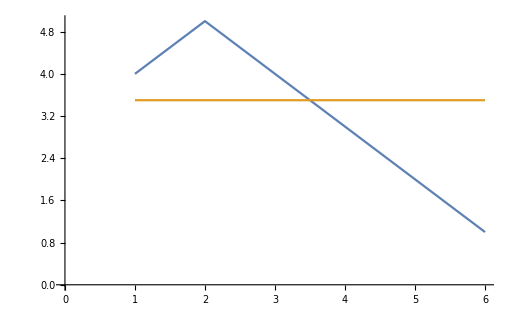

```mathematica
ListLinePlot@{{4,5,4,3,2,1},{3.5,3.5,3.5,3.5,3.5,3.5}}
```

```mathematica
Grid[
{
{Style["Input 1",Bold],Style["Input 2",Bold],Style["Output",Bold]},
{False,False,False},
{False,True,True},
{True,False,True},
{True,True,False}},
Frame->All]
```

Input 1 | Input 2 | Output
False | False | False
False | True | True
True | False | True
True | True | False

```mathematica
{{True,False},{False,True}}
```

```mathematica
Grid[
{
{Style["Tsetlin Automaton State",Bold],Style["Include?",Bold],Style["Input",Bold],Style["Negated input?",Bold],Style["Final Result",Bold]},
{4,Yes,True,"No",True},
{3,No,False,"No",""},
{3,No,False,"Yes",""},
{4,Yes,True,"Yes","True"}
},
Frame->All]
```

Tsetlin Automaton State | Include? | Input | Negated input? | Final Result
4 | Yes | True | No | True
3 | No | False | No | 
3 | No | False | Yes | 
4 | Yes | True | Yes | True

```mathematica
Grid[
{
{Style["Clause input",Bold],Style["Clause include corresponding input?",Bold],Style["Clause included input",Bold],Style["Clause output",Bold]},
{{True,False,False,True},{"Yes","No","No","Yes"},{True,True},True},
{{True,False,False,True},{"No","No","Yes","Yes"},{False,True},False}
},
Frame->All]
```

Clause input | Clause include corresponding input? | Clause included input | Clause output
{True,False,False,True} | {Yes,No,No,Yes} | {True,True} | True
{True,False,False,True} | {No,No,Yes,Yes} | {False,True} | False

```mathematica
Grid[
Transpose@
{
{Style["Clause 1 output",Bold],Style["Clause 2 output",Bold],Style["Output function",Bold],Style["Final output",Bold]},
{True,False,"OR",True}
},
Frame->All]
```

Clause 1 output | True
Clause 2 output | False
Output function | OR
Final output | True